## Initialization

### Import dependencies

```mathematica
(* Run bubble-4a-murphree.nb before. *)
```

```mathematica
packageDirectory=FileNameJoin@{NotebookDirectory[],"mathematica_packages\\"}
outputDirectory=FileNameJoin@{NotebookDirectory[],"output\\"}
```

G:\My Drive\bubble_bec\mathematica_packages

G:\My Drive\bubble_bec\output

```mathematica
If[Not@MemberQ[$Path,packageDirectory],
AppendTo[$Path,packageDirectory];
]
```

```mathematica
Get["MovingTrap-murphree.m"]
Get["FitCurveHacked-mean-murphree.m"]
```

The following variables used by ExpansionPlotHacked are protected by this package: {axis, trap, usemodel, frequency, trapposition, gridlines, size, meanfrequency, meanmodel}

### Define initial and final trap parameters

These values taken from SM3 “predictions”

```mathematica
(** Current to field magnitude conversion factors for Bias **)
BxCalib=40.625;(*[G/A]*)
ByCalib=14.286;(*[G/A]*)
BzCalib=-10.368;(*[G/A]*)

(** Max current values **)
(* Chip *)
IlbMax=3.5; (* [A] *)
IzbMax=-3.5;(* [A] *)
IhMax=5.;(* [A] *)

(* Bias coils *)
IbxMax=8.;(*[A]*)
IbyMax=3.02;(*[A]*)
IbzMax=3.;(*[A]*)

(** Table values **)
(* These were taken from CAL3A_chiptrap_v1.pdf *)
(* Initial trap *)
tableZLHb={
(* Chip *)
AZ1=0.243,(* % *)
AZ2=-0.686,(* % *)
H1pH2=0.46,(* % *) 

(* Bias coils *)
T1=0.0275,(*%*)
T2=T1,
Y=0.85,(*%*)
Z=-0.05(*%*)
};

fdec=0.2;
tableZLHbDecomp={
(* Chip *)
tableZLHb⟦1⟧, (* AZ1 [%] *)
tableZLHb⟦2⟧,(* AZ2 [%] *)
tableZLHb⟦3⟧,(* H1pH2 [%] *)

(* Bias coils *)
fdec*tableZLHb⟦4⟧,(* T1 [%] *)
fdec*tableZLHb⟦5⟧,(* T2 [%] *)
fdec*tableZLHb⟦6⟧,(* Y [%] *)
fdec*tableZLHb⟦7⟧(* Z [%] *)
};

tableZHb={
(* Chip *)
0., (* AZ1 [%] *)
-0.743, (* AZ2 [%] *)
0.46, (* H1pH2 [%] *)

(* Bias coils *)
-0.018, (* T1 [%] *)
-0.018, (* T2 [%] *)
0.63,(* Y [%] *)
-0.0001 (* Z [%] *)
};

tableZHbC={
(* Chip *)
0., (* AZ1 [%] *)
0.914, (* AZ2 [%] *)
0.26, (* H1pH2 [%] *)

(* Bias coils *)
-0.006125,(* T1 [%] *)
-0.006125,(* T2 [%] *)
0.0677, (* Y [%] *)
-0.11367 (* Z [%] *)
};

(* Trap CurrL, CurrZ, CurrH, Bx1, By1, Bz1 *)
defineTableFromTrap[trap_]:=Module[
{CurrL=trap⟦1⟧,
CurrZ=trap⟦2⟧,
CurrH=trap⟦3⟧,
Bx1=trap⟦4⟧,
By1=trap⟦5⟧,
Bz1=trap⟦6⟧,
table},

table={
CurrL/IlbMax, (*AZ1 [%]*)
CurrZ/IzbMax, (*AZ2 [%]*)
CurrH/IhMax, (*H1pH2 [%]*)

Bx1/(-1.*IbxMax*BxCalib), (*T1*)
Bx1/(-1.*IbxMax*BxCalib), (*T2*)
By1/(IbyMax*ByCalib), (*Y*)
Bz1/(IbzMax*BzCalib) (*Z*)
};
Return[table];
];

defineTrapFromTable[table_]:=Module[
{AZ1=table⟦1⟧,
AZ2=table⟦2⟧,
H1pH2=table⟦3⟧,
T1=table⟦4⟧,
T2=table⟦5⟧, (* Currently T2=T1, and so doesn't play role yet *)
Y=table⟦6⟧,
Z=table⟦7⟧,
trap},

trap={
(* Chip *)
AZ1*IlbMax,(*Ilb0 [A]*)
AZ2*IzbMax,(*Izb0 [A]*)
H1pH2*IhMax,(*Ih0 [A]*)

(* Bias coils *)
(-1.)*T1*IbxMax*BxCalib,(*Bx [G]*)
Y*IbyMax*ByCalib,(*By [G]*)
Z*IbzMax *BzCalib(*Bz [G]*)
};
Return[trap];
]

(* The Bates trap *)
currLa=0;
currZa=0;
currLb=0;
currZb=2.6;
currH = 2.6;

Bx1 = (-0.048)*40.625;
By1 = (0.43)*14.286;
Bz1 = (0.3003)*(-10.3675);

trapZHbB={currLa,currZa,currLb,currZb,currH,Bx1,By1,Bz1};
tableZHbB=convertTrapParametersToCALTable[trapZHbB,verbose->True];
(* *)

(* Package for resale: *)
(* Compare these values to those in SM3 "predictions", although Bzfinal, for us, should be multiplied by 0.2 *)
trapzero=defineTrapFromTable[tableZLHb]
trapone=trapZHbB⟦3;;⟧
(*trapone=defineTrapFromTable@defineTableFromTrap@{CurrL,CurrZ,CurrH,Bx1,By1,Bz1}*)
```

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0,2.6,2.6,-1.95,6.14298,-3.11336}

### Define target ramp analytic function

```mathematica
cass[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2 t^(1/4) -1)]/Tanh[5];
cassShort[ωi_,ωf_,t_]:=(ωi+ωf)/2+(ωf-ωi)/2 Tanh[5(2(t/2)^(1/4) -1)]/Tanh[5];
```

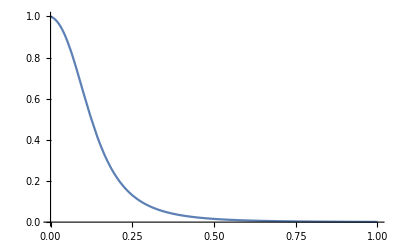

```mathematica
Plot[cassShort[1,0,t],{t,0,1},PlotRange->All]
```

```mathematica
trapAnalytic[trap1_,trap2_,t_]:=trap1+(trap2-trap1)*(1-cassShort[1,0,t]);
zeroCrossing[trap1_,trap2_]:=(1/8)*((1/5)*ArcTanh[2*Tanh[5]*((1/2)-trap2[[6]]/(trap2[[6]]-trap1[[6]]))]+1)^4;
```

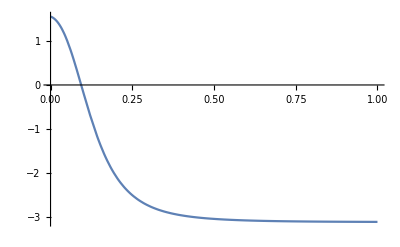

0.0937468

tZero = 0.0468734

```mathematica
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All]
tauZero=zeroCrossing[trapzero,trapone]
period=500*10^(-3);
deltaTau=10*^-3/period;
newTaus={tauZero-deltaTau,tauZero,tauZero+deltaTau};
Print["tZero = "<>ToString[tauZero*period]]
```

```mathematica
Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,rampin1sguess⟦1⟧}]
```

{{0.02,1.44003},{0.02,1.44003},{0.02,1.44003},{0.014,1.48744},{0.02,1.44003},{0.02,1.44003},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.03,1.33414},{0.036,1.25423},{0.05,1.02162},{0.08,0.350223},{0.14,-1.11223},{0.16,-1.49802},{0.18,-1.81564}}

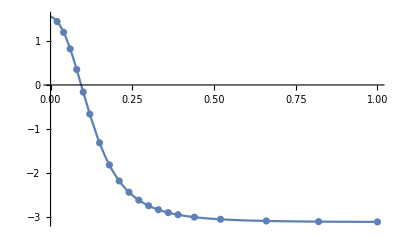

```mathematica
Show[{
Plot[trapAnalytic[trapzero,trapone,t]⟦6⟧,{t,0,1},PlotRange->All],
ListPlot[Table[{t,trapAnalytic[trapzero,trapone,t]⟦6⟧},{t,Accumulate@rampin1sguess⟦1⟧}]]
}]
```

### Define ramp ansatz

#### Trap 1 Short

```mathematica
rampin1sguess={{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.014,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.036,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
rampin1sguess={2*{0.01,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.015,0.025,0.04,0.07,0.08,0.09},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.01982,0.04078,0.06357,0.08265,0.09264,0.09506,0.13261,0.111,0.08766,0.06631,0.05043,0.03763,0.02784,0.02086,0.01544,0.01839,0.01684,0.01298,0.0052,0.00229}}

```mathematica
Table[Total@#[[1,1;;m]],{m,Length@#[[1]]}]&[rampin1sguess]
```

{0.02,0.04,0.06,0.08,0.1,0.12,0.15,0.18,0.21,0.24,0.27,0.3,0.33,0.36,0.39,0.44,0.52,0.66,0.82,1.}

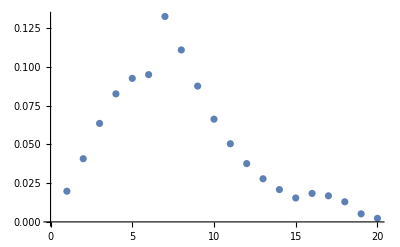

```mathematica
ListPlot[rampin1sguess⟦2⟧]
```

```mathematica
(*rampin1sguess⟦1,9;;13⟧
rampin1sguess⟦1⟧=Join[rampin1sguess⟦1,1;;9⟧,{0.01,0.01,0.01,0.01,0.01},rampin1sguess⟦1,10;;⟧]
rampin1sguess⟦1,9;;18⟧
rampin1sguess⟦1,9;;18⟧={0.02,0.02,0.02,0.01,0.01,0.01,0.01,0.01,0.02,0.02}*)
```

```mathematica
(*rampin1sguess⟦2,9;;13⟧
rampin1sguess⟦2⟧=Join[rampin1sguess⟦2,1;;9⟧,ConstantArray[0.,5],rampin1sguess⟦2,10;;⟧]*)
```

```mathematica
(*rampin1sguess*)
```

```mathematica
Total[rampin1sguess⟦1⟧]
```

1.

```mathematica
Total[rampin1sguess⟦2⟧]
```

1.

```mathematica
Length@rampin1sguess[[1]]
```

20

## Calculate ramp

```mathematica
nramps1short=Length@rampin1sguess⟦1⟧
```

20

The following took 8 1/2 minutes to complete. (1 1/4 hr on the Dell)

```mathematica
(* 
If FitCurveHacked runs in less than a second and has multiple errors citing GeometricMean, go back and make sure bubble-4a.nb was run before this notebook. MovingTrap-murphree.m calls ChipTrapFrequencies, which is defined in that notebook.
*)
```

```mathematica
(rampin1s=FitCurveHacked[trapzero,trapone,rampin1sguess,nramps1short,-3.5,-5])//Timing
```

{0.50991,-253.96,0.00001}

Completed point 1 of 19 in 47.6406 s (Total time: 0.79401 min).

{0.51023,-240.867,0.00001}

{0.0435,-0.155742,0.00001}

Completed point 2 of 19 in 54.75 s (Total time: 1.70651 min).

{0.50004,-221.23,0.00001}

{0.06598,-0.239832,0.00001}

Completed point 3 of 19 in 72.75 s (Total time: 2.91901 min).

{0.06178,10.6021,0.00001}

{0.07208,5.12106,0.00001}

{0.07723,2.38178,0.00001}

{0.0798,1.01515,0.00001}

{0.08109,0.329277,0.00001}

{0.08173,-0.0109783,0.00001}

Completed point 4 of 19 in 50.125 s (Total time: 3.75443 min).

{0.0693,10.656,0.00001}

{0.08085,4.57943,0.00001}

{0.08663,1.54416,0.00001}

{0.08952,0.0280088,0.00001}

Completed point 5 of 19 in 32.2031 s (Total time: 4.29115 min).

{0.07126,9.35157,0.00001}

{0.08314,3.2708,0.00001}

{0.08908,0.241514,0.00001}

{0.09205,-1.27024,0.00001}

Completed point 6 of 19 in 43.2813 s (Total time: 5.0125 min).

{0.09972,11.0911,0.00001}

{0.11634,3.14242,0.00001}

{0.12465,-0.79402,0.00001}

{0.12258,0.184104,0.00001}

{0.12362,-0.307524,0.00001}

Completed point 7 of 19 in 44.7344 s (Total time: 5.75807 min).

{0.08409,8.18492,0.00001}

{0.0981,2.13175,0.00001}

{0.10511,-0.858682,0.00001}

{0.10336,-0.114578,0.00001}

{0.10292,0.0727674,0.00001}

{0.10314,-0.0209178,0.00001}

Completed point 8 of 19 in 50.8438 s (Total time: 6.60547 min).

{0.06714,6.30249,0.00001}

{0.07833,2.00808,0.00001}

{0.08392,-0.108083,0.00001}

{0.08252,0.420072,0.00001}

{0.08322,0.155841,0.00001}

{0.08357,0.0238404,0.00001}

Completed point 9 of 19 in 46.4375 s (Total time: 7.37943 min).

{0.05153,5.17477,0.00001}

{0.06012,2.24252,0.00001}

{0.06441,0.795871,0.00001}

{0.06656,0.0753019,0.00001}

{0.06763,-0.282202,0.00001}

Completed point 10 of 19 in 44.8125 s (Total time: 8.1263 min).

{0.03976,3.85685,0.00001}

{0.04639,1.82018,0.00001}

{0.0497,0.813424,0.00001}

{0.05136,0.311029,0.00001}

{0.05219,0.0604568,0.00001}

{0.0526,-0.0631665,0.00001}

Completed point 11 of 19 in 46.2969 s (Total time: 8.89792 min).

{0.11083,-18.2181,0.00001}

Completed point 12 of 19 in 38.9375 s (Total time: 9.54688 min).

{0.08564,-13.4772,0.00001}

{0.03112,0.0286497,0.00001}

{0.03122,0.00251892,0.00001}

Completed point 13 of 19 in 47.8281 s (Total time: 10.344 min).

{0.06648,-10.1888,0.00001}

{0.02388,-0.0117728,0.00001}

Completed point 14 of 19 in 59. s (Total time: 11.3273 min).

{0.05179,-7.80525,0.00001}

Completed point 15 of 19 in 40.375 s (Total time: 12.0003 min).

{0.04417,-5.06415,0.00001}

{0.02186,-0.0597957,0.00001}

Completed point 16 of 19 in 40.9844 s (Total time: 12.6833 min).

{0.0325,-2.63926,0.00001}

{0.02027,0.0101762,0.00001}

Completed point 17 of 19 in 30.4375 s (Total time: 13.1906 min).

{0.02022,-0.900467,0.00001}

{0.01576,0.0366725,0.00001}

{0.01593,0.000744748,0.00001}

Completed point 18 of 19 in 33.5313 s (Total time: 13.7495 min).

{0.00807,-0.277681,0.00001}

Completed point 19 of 19 in 17.4531 s (Total time: 14.0404 min).

{846.641,{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.04304,0.06555,0.08173,0.08952,0.08945,0.1231,0.10314,0.08357,0.06683,0.0524,0.04056,0.03122,0.02388,0.01813,0.02159,0.02027,0.01593,0.00678,0.00301}}}

```mathematica
rampin1s⟦2⟧-rampin1sguess⟦2⟧
```

{0.00048,0.00226,0.00198,-0.00092,-0.00312,-0.00561,-0.00951,-0.00786,-0.00409,0.00052,0.00197,0.00293,0.00338,0.00302,0.00269,0.0032,0.00343,0.00295,0.00158,0.00072}

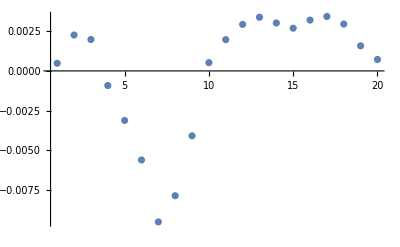

```mathematica
ListPlot[%,PlotRange->All]
```

The following took ~4 1/2 minutes to run. (~ 1 hr 12 min on Dell)

```mathematica
points1s=100;
(pts1s=MovingTrap[trapzero,trapone,rampin1s,points1s,nramps1short];)//Timing
```

{355.719,Null}

### Plot calculated ramp’s parameters

{{0.,1.},{3.83329,6.83513}}

{46.2145,929.95}

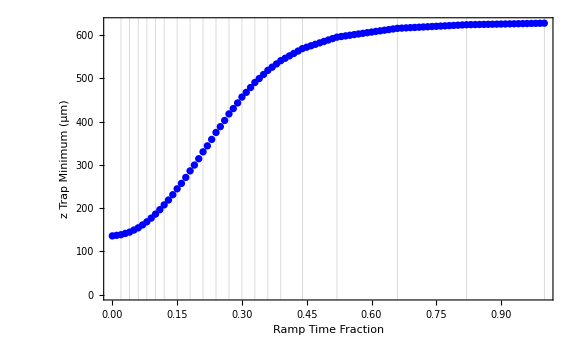
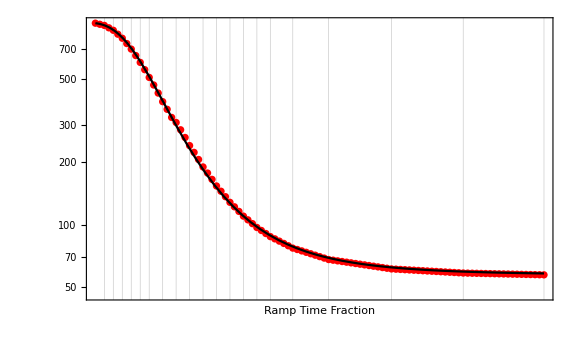

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"z"]
```

{{0.,1.},{2.99006,4.77009}}

{19.8868,117.929}

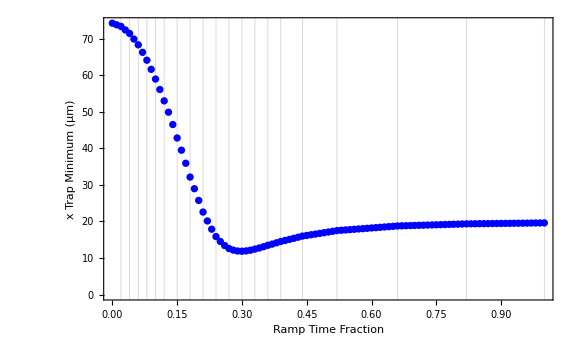
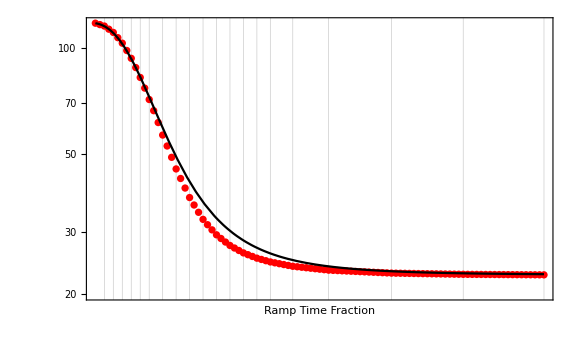

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"x",meanfrequency->False]
```

{{0.,1.},{3.77149,6.87598}}

{43.4445,968.724}

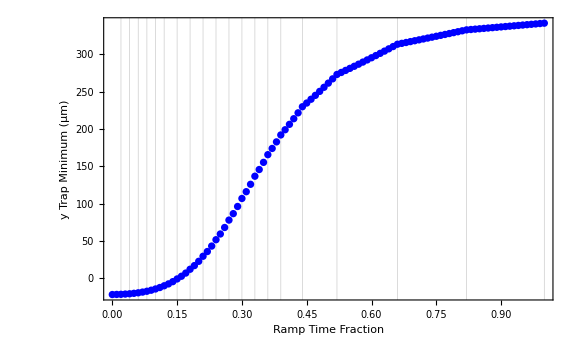
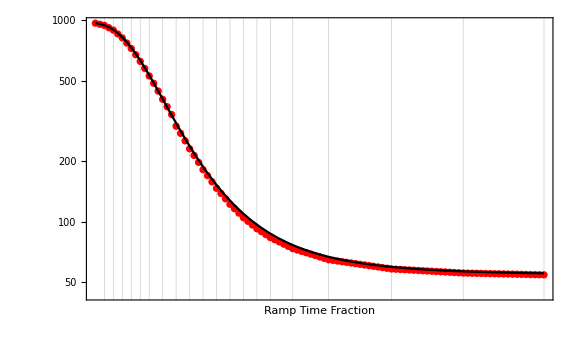

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->True,frequency->True,gridlines->True,usemodel->True,size->Large,axis->"y",meanfrequency->False]
```

{{0.,1.},{3.83329,6.83513}}

{46.2145,929.95}

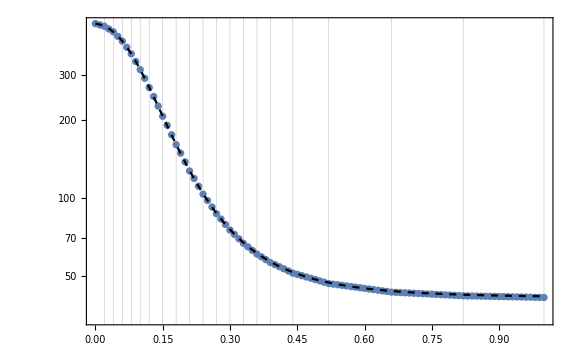

```mathematica
ExpansionPlotHacked[pts1s,points1s,rampin1s,trap-> "1",trapposition->False,frequency->False,gridlines->True,usemodel->True,size->Large,axis->"z",meanfrequency->True,meanmodel->True]
```

```mathematica
Beep[]
```

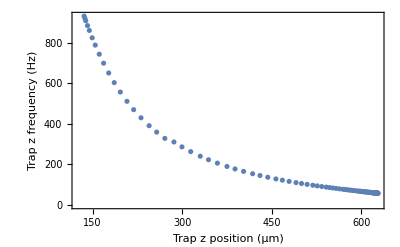

```mathematica
plotZFreqVZmin[movingtrap_]:=Module[{zs,omegas},
zs[n_]:=movingtrap⟦n,1,3⟧*10^6;
omegas[n_]:=movingtrap⟦n,2,3⟧;

ListPlot[Table[{zs[n],omegas[n]},{n,Range[Length[movingtrap]]}],Frame->True,FrameLabel->{"Trap z position (μm)","Trap z frequency (Hz)"}]
]
plotZFreqVZmin[pts1s]
```

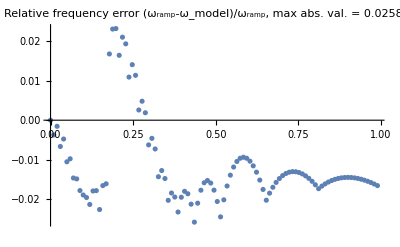

```mathematica
plotFreqError[pts1s]
```

```mathematica
printTrapParameters[{{minx_,miny_,minz_},{omegax_,omegay_,omegaz_},bmin_}]:=Print[
"Position = "<>ToString[{minx,miny,minz}*10^6]<>" μm\n"<>
"Frequency = "<>ToString[{omegax,omegay,omegaz}]<>" Hz\n"<>
"Bmin = "<>ToString[bmin]<>" G"];

printTrapParameters[pts1s⟦1⟧]
printTrapParameters[pts1s⟦-1⟧]
```

Position = {74.2507, -21.9915, 135.717} μm
Frequency = {117.929, 968.724, 929.95} Hz
Bmin = 8.97843 G

Position = {19.6048, 341.948, 627.837} μm
Frequency = {22.6293, 54.4236, 57.4638} Hz
Bmin = 4.98191 G

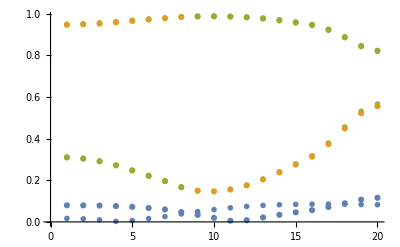

```mathematica
plotTrapPrincAxes[trap1_,trap2_,rampin_]:=Module[
{nramps=Length@rampin⟦1⟧,
eVecIndex,
characVtime,
vec2Plot,vec3Plot},
characVtime=Table[SingleTrapCharacteristics[trap1,trap2,rampin,nramps,n],{n,nramps}];
eVecIndex=2;
vec2Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}],PlotMarkers->"OpenMarkers"];
eVecIndex=3;
vec3Plot=ListPlot[Table[Abs@characVtime⟦All,eVecIndex,1,vecComp⟧,{vecComp,Range[3]}]];
Show[vec2Plot,vec3Plot]
]
plotTrapPrincAxes[trapzero,trapone,rampin1s]
```

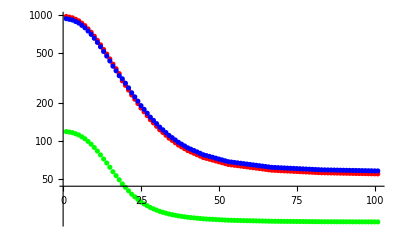

```mathematica
plotTrapYandZCharacteristics[movingramp_]:=Module[
{xFreqs=movingramp⟦All,2,1⟧,
yFreqs=movingramp⟦All,2,2⟧,
zFreqs=movingramp⟦All,2,3⟧,
xPlot,yPlot,zPlot},
xPlot=ListLogPlot[xFreqs,PlotStyle->Green];
yPlot=ListLogPlot[yFreqs,PlotStyle->Red];
zPlot=ListLogPlot[zFreqs,PlotStyle->Blue];
Show[yPlot,zPlot,xPlot,PlotRange->All]
]
plotTrapYandZCharacteristics[pts1s]
```

## Export ramp

### Export ramp

```mathematica
trap1short={#⟦1⟧,Table[Total[Take[Round[#⟦2⟧,10.^-5],n]],{n,Length@rampin1s⟦1⟧}]}&[rampin1s]
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.06334,0.12889,0.21062,0.30014,0.38959,0.51269,0.61583,0.6994,0.76623,0.81863,0.85919,0.89041,0.91429,0.93242,0.95401,0.97428,0.99021,0.99699,1.}}

```mathematica
(* Set the DateStringFormat to help create unique names for each exported beam.The format is inspired by the ISO 8601 standard. *)
generateTimeStamp[]:=DateString[{"Year","Month","Day","T","Hour","Minute","Second"}];
rampTimeStamp=generateTimeStamp[]
```

20200824T121206

```mathematica
Export[FileNameJoin@{outputDirectory,rampTimeStamp<>"_trap1short.csv"},trap1shortᵀ]
```

G:\My Drive\bubble_bec\output\20200824T121206_trap1short.csv

### Export ramp parameters

```mathematica
exportRampEndpoints[trap1_,trap2_,rampTimeStamp_,outputDirectory_]:=Module[
{
fileName=rampTimeStamp<>"_ramp_endpoints",
table={trap1,trap2},
headings={{"InitialTrap","FinalTrap"},{"IL[A]","IZ[A]","IH[A]","Bx[G]","By[G]","Bz[G]"}}
},
Print[table];
Export[FileNameJoin@{outputDirectory,fileName<>".csv"},table,TableHeadings->headings]
]

exportRampEndpoints[trapzero,trapone,rampTimeStamp,outputDirectory]
```

{{0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0,2.6,2.6,-1.95,6.14298,-3.11336}}

G:\My Drive\bubble_bec\output\20200824T121206_ramp_endpoints.csv

```mathematica
Beep[];
Pause[1];
Beep[];
```

```mathematica
defineTableFromTrap[trapone]
```

{0.,-0.742857,0.52,0.006,0.006,0.142384,0.100095}

## Look at intermediate trap and CAL table values

{{0., 0.8505}, {0.01, 0.841867}, {0.02, 0.833235}, {0.03, 0.814932}, {0.04, 0.796629}, {0.05, 0.768754}, {0.06, 0.740879}, {0.07, 0.706123}, {0.08, 0.671368}, {0.09, 0.633299}, {0.1, 0.595231}, {0.11, 0.557192}, {0.12, 0.519154}, {0.13, 0.484255}, {0.14, 0.449356}, {0.15, 0.414457}, {0.16, 0.385217}, {0.17, 0.355977}, {0.18, 0.326737}, {0.19, 0.303044}, {0.2, 0.279352}, {0.21, 0.25566}, {0.22, 0.236714}, {0.23, 0.217768}, {0.24, 0.198821}, {0.25, 0.183966}, {0.26, 0.169111}, {0.27, 0.154255}, {0.28, 0.142756}, {0.29, 0.131258}, {0.3, 0.119759}, {0.31, 0.110908}, {0.32, 0.102057}, {0.33, 0.0932063}, {0.34, 0.0864363}, {0.35, 0.0796663}, {0.36, 0.0728964}, {0.37, 0.0677565}, {0.38, 0.0626166}, {0.39, 0.0574768}, {0.4, 0.0538043}, {0.41, 0.0501319}, {0.42, 0.0464594}, {0.43, 0.042787}, {0.44, 0.0391145}, {0.45, 0.0369595}, {0.46, 0.0348046}, {0.47, 0.0326496}, {0.48, 0.0304947}, {0.49, 0.0283397}, {0.5, 0.0261848}, {0.51, 0.0240298}, {0.52, 0.0218749}, {0.53, 0.0209071}, {0.54, 0.0199394}, {0.55, 0.0189716}, {0.56, 0.0180039}, {0.57, 0.0170361}, {0.58, 0.0160684}, {0.59, 0.0151006}, {0.6, 0.0141329}, {0.61, 0.0131651}, {0.62, 0.0121974}, {0.63, 0.0112296}, {0.64, 0.0102619}, {0.65, 0.00929414}, {0.66, 0.00832639}, {0.67, 0.007966}, {0.68, 0.0076056}, {0.69, 0.0072452}, {0.7, 0.0068848}, {0.71, 0.0065244}, {0.72, 0.006164}, {0.73, 0.0058036}, {0.74, 0.0054432}, {0.75, 0.0050828}, {0.76, 0.0047224}, {0.77, 0.004362}, {0.78, 0.0040016}, {0.79, 0.0036412}, {0.8, 0.0032808}, {0.81, 0.0029204}, {0.82, 0.00256}, {0.83, 0.00241778}, {0.84, 0.00227556}, {0.85, 0.00213334}, {0.86, 0.00199112}, {0.87, 0.00184889}, {0.88, 0.00170667}, {0.89, 0.00156445}, {0.9, 0.00142222}, {0.91, 0.00128}, {0.92, 0.00113778}, {0.93, 0.000995558}, {0.94, 0.000853335}, {0.95, 0.000711112}, {0.96, 0.00056889}, {0.97, 0.000426667}, {0.98, 0.000284445}, {0.99, 0.000142222}, {1., 0.}}

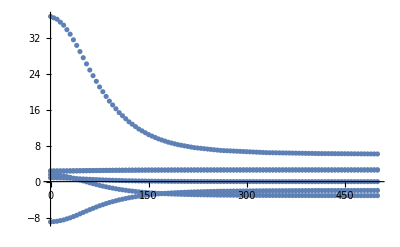

```mathematica
listRampCALTables[trap1_,trap2_,rampin_,npoints_,nramps_:3]:=Module[
{
deltatrap=trap1-trap2,
ramp=Prepend[Table[{Sum[#[[1,i]],{i,n}],Sum[#[[2,i]],{i,n}],#[[2,n]]/#[[1,n]]},{n,nramps}]&[rampin],{0,0,0}],
ramplist,
colors={"Red","Orange","Yellow","Green","Blue","Black"}
},

ramplist=Prepend[Drop[Table[{t,Piecewise[Table[{#3-(#1[[n-1,2]]+#1[[n,3]]*(t-#1[[n-1,1]]))*#2,#1[[n-1,1]]<t<=#1[[n,1]]},{n,2,nramps+1}]&[ramp,deltatrap,trap1]]},{t,0.,1.,1./npoints}],1],{0.,trap1}];

Print[ToString[{#[[1]],#[[2,1]]}&/@ramplist]];

Return[Table[ListPlot[{#⟦1⟧*500,#⟦2,k⟧}&/@ramplist,PlotStyle->colors⟦k⟧],{k,6}]];
];
test=listRampCALTables[trapzero,trapone,rampin1s,points1s,nramps1short];
Show[test,PlotRange->All]
```

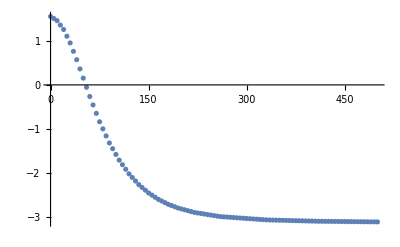

```mathematica
test[[6]]
```

```mathematica
rampin1s
```

{{0.02,0.02,0.02,0.02,0.02,0.02,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.03,0.05,0.08,0.14,0.16,0.18},{0.0203,0.04304,0.06555,0.08173,0.08952,0.08945,0.1231,0.10314,0.08357,0.06683,0.0524,0.04056,0.03122,0.02388,0.01813,0.02159,0.02027,0.01593,0.00678,0.00301}}

```mathematica
plotRampCALTable[trap1_,trap2_,rampin_]:=Module[
{
deltaTrap=trap2-trap1,
totRamp=Table[{Total@rampin⟦1,1;;k⟧,Total@rampin⟦2,1;;k⟧},{k,Length@rampin⟦1⟧}]~Prepend~{0,0},
trapRamp
},
trapRamp=Table[(totRamp⟦k,2⟧*deltaTrap+trap1)~Prepend~totRamp⟦k,1⟧,{k,Length@rampin⟦1⟧+1}];
Return[trapRamp];
];
trapRamp=plotRampCALTable[trapzero,trapone,rampin1s]
trapzero
trapone
```

{{0,0.8505,2.401,2.3,-8.9375,36.6722,1.5552},{0.02,0.833235,2.40504,2.30609,-8.79565,36.0524,1.46043},{0.04,0.796629,2.4136,2.319,-8.49491,34.7384,1.25949},{0.06,0.740879,2.42665,2.33867,-8.03688,32.7373,0.953469},{0.08,0.671368,2.44291,2.36319,-7.46579,30.2421,0.571908},{0.1,0.595231,2.46073,2.39004,-6.84027,27.5091,0.153978},{0.12,0.519154,2.47853,2.41688,-6.21524,24.7783,-0.263624},{0.15,0.414457,2.50303,2.45381,-5.35508,21.0202,-0.838324},{0.18,0.326737,2.52355,2.48475,-4.63439,17.8714,-1.31984},{0.21,0.25566,2.54018,2.50982,-4.05044,15.3201,-1.70999},{0.24,0.198821,2.55348,2.52987,-3.58347,13.2798,-2.02199},{0.27,0.154255,2.56391,2.54559,-3.21732,11.6801,-2.26662},{0.3,0.119759,2.57198,2.55776,-2.93391,10.4418,-2.45598},{0.33,0.0932063,2.57819,2.56712,-2.71576,9.48867,-2.60173},{0.36,0.0728964,2.58294,2.57429,-2.5489,8.75964,-2.71322},{0.39,0.0574768,2.58655,2.57973,-2.42222,8.20614,-2.79786},{0.44,0.0391145,2.59085,2.5862,-2.27136,7.54702,-2.89865},{0.52,0.0218749,2.59488,2.59228,-2.12972,6.92819,-2.99328},{0.66,0.00832639,2.59805,2.59706,-2.01841,6.44186,-3.06766},{0.82,0.00256,2.5994,2.5991,-1.97103,6.23487,-3.09931},{1.,0.,2.6,2.6,-1.95,6.14298,-3.11336}}

{0.8505,2.401,2.3,-8.9375,36.6722,1.5552}

{0,2.6,2.6,-1.95,6.14298,-3.11336}

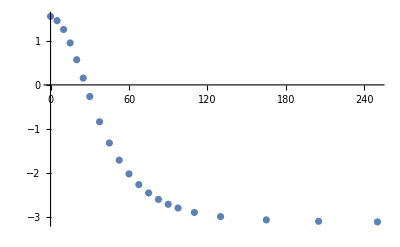

```mathematica
ListPlot[{#[[1]]*250,#[[7]]}&/@trapRamp]
```

```mathematica
Total@{1,2,3,4,5}
```

15